```mathematica
<< VarCleanup`;
<< PenduloComPolia`Importador`;
<< PenduloComPolia`ModeloEDO`;
<< PenduloComPolia`ModeloGeometrico`;
```

```mathematica
VarCleanup`RemoveGlobal[];
```

Remove::rmnsm: There are no symbols matching "Global`*".

## Linearizar θ[ϕ]

```mathematica
xGeom[θ_]=X[r, L0, θ];
yGeom[θ_]=Y[r,L0,θ];
```

```mathematica
ϕ[θ_]=ArcTan[xGeom[θ],yGeom[θ]];
```

```mathematica
thetaParaPhi[theta_] = ϕ[theta*π/180]/Degree;
lista = Table[{i, thetaParaPhi[i]}, {i,-45,+45,0.1}];
modeloLinear[raio_, comprimento_] := Module[{theta},
LinearModelFit[lista/.{r->raio,L0->comprimento}, theta,theta]
]
```

```mathematica
Manipulate[
Show[
Plot[thetaParaPhi[theta]/.{r->raio,L0->comprimento}, {theta,-45,45}, AxesLabel->{"θ","ϕ"}],
Plot[modeloLinear[raio,comprimento][theta], {theta, -45,45}]
],
{raio,0.078,1},
{comprimento,0.30,1}
]
```

## Modelo matemático por EDOs

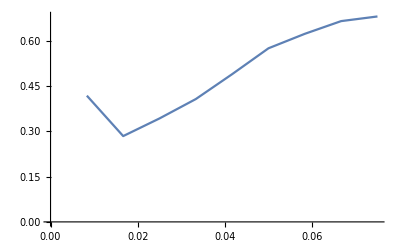

```mathematica
thetaExp = Listar[2,"t","θ"];
omegaInicial= Table[{thetaExp[[i]][[1]],(thetaExp[[i]][[2]]-thetaExp[[1]][[2]])/(thetaExp[[i]][[1]]-thetaExp[[1]][[1]])},{i,2,10}];
ListLinePlot[omegaInicial]
```

### Gráfico

```mathematica
Manipulate[
Module[{θ},
θ[tempo_]=Quiet[Module[{t},
ReplaceAll[SolucaoNumerica[{Θ[0]== (#[[1]]&)@Listar[2, "θ"], Θ'[0]==omegaInicial},{t, 0, 8}],{t->tempo}]
]];
Show[
Plot[θ[t], {t,0,8}, PlotStyle->Blue],
ListLinePlot[Listar[2,"t","θ"], PlotStyle->Red],
PlotRange->{{0,9},{-0.7,0.7}},
Background->Automatic,
ImageSize->Full
]
],
{omegaInicial, -5,1}
]
```

## Tomadas

```mathematica
x = Listar[2,"t", "x", "y"];
```

Comparar com uma teórica

```mathematica
Clear[posicoesX]
```

```mathematica
θ[tempo_]=Quiet[Module[{t},
ReplaceAll[SolucaoNumerica[{Θ[0]== (#[[1]]&)@Listar[2, "θ"], Θ'[0]==0.42},{t, 0, 8}],{t->tempo}]
]];
```

```mathematica
tempos = Listar[2, "t"];
posicoesX[tempo_] = X[Pegar["raio da polia"],0.29,theta[t]]/.theta[t]->θ[tempo];
posicoesY[tempo_] = Y[Pegar["raio da polia"],0.29,theta[t]]/.theta[t]->θ[tempo];
```

```mathematica
tabelaX = Table[{Part[tempos,i],posicoesX[Part[tempos,i]]}//Flatten,{i,1,800}];
```

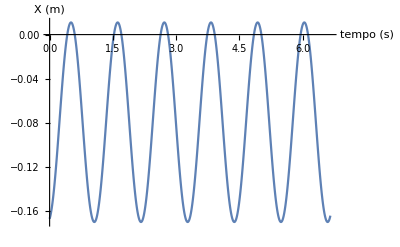

```mathematica
ListLinePlot[tabelaX, AxesLabel->{"tempo (s)","X (m)"}]
```

### Teste

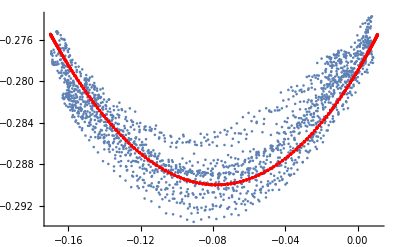

```mathematica
Show[
ListPlot[Listar[2,"x","y"]],
ListPlot[Table[{posicoesX[tempo],posicoesY[tempo]},{tempo,0,8,0.01}],PlotStyle->Red],
PlotRange->All,
ImageSize->Full
]
```